```mathematica
(* if n2 = 0*)
Binomial[20,0]
```

1

```mathematica
(* if n2 = 1*)
Binomial[19,1]
```

19

```mathematica
(* if n2 = 2 *)

Binomial[18,2]
```

153

```mathematica
Sum[Binomial[20-i,i],{i,0,10,1}]
```

10946

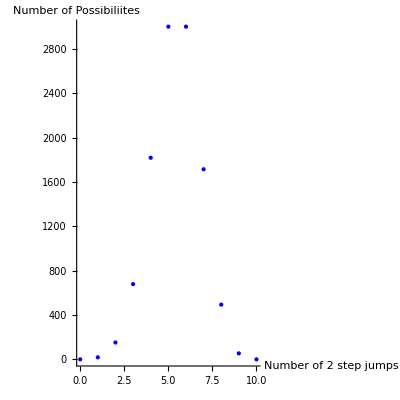

```mathematica
Show[Graphics[{Blue,PointSize[Large],Point[Table[{x,Binomial[20-x,x]},{x,0,10,1}]]}],Axes->True,AspectRatio->1,AxesLabel->{"Number of 2 step jumps","Number of Possibiliites"}]
```

```mathematica
Sum[If[20-2i-2j >0 && 20-i-2j >0,Binomial[20-i-2j,i]*Binomial[20-i-2j-i,j],0],{i,0,10,1},{j,0,7,1}]
```

121414

```mathematica
f[n_]=Sum[If[20-Sum[-
```